```mathematica
(*Limpieza de las variables y el kernel de Mthematica*)
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
ds=Import["https://raw.githubusercontent.com/EisaacJC/COVID-19/master/DATOS%20COVID19.csv"];
```

```mathematica
key$ds=ds[[1]];
```

```mathematica
data=Dataset[Map[AssociationThread[key$ds->#]&,ds[[2;;]]]]
```

Dataset[<>]

```mathematica
fecha[dateString_: String]:=DateObject[{dateString,{"Day","Month","YearShort"}},"Day"]
```

```mathematica
data=data[All, {"Fecha"-> fecha}]
```

Dataset[<>]

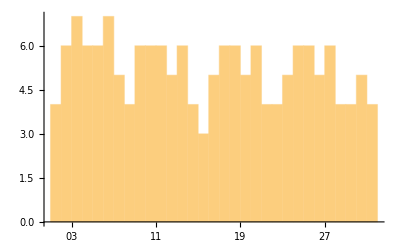

```mathematica
(*Distribución de reportes numéricos por día de mes*)data[DateHistogram[#,"Day",DateReduction->"Month"]&,"Fecha"]
```

```mathematica
key$ds
```

{Fecha,S&P/BMV IPC (MXX) CIERRE,S&P/BMV IPC (MXX) APERTURA,S&P/BMV IPC (MXX) VOL,NASDAQ CIERRRE,NASDAQ APERTURA,NASDAQ VOL,S&P 500 CIERRE,RUSELL 2000 CIERRE,RUSELL 2000 APERTURA,DOLAR CIERRE,DOLAR APERTURA,EURO CIERRE,EURO APERTURA,TITULAR MUNDIAL,UBICACIÓN,LINK MUNDIAL,Fecha ref 2,CONFIRMADOS MUNDO,CONFIRMADOS MEXICO,CONFIRMADOS USA}

```mathematica
confUSA=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS USA"];
confMEX=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS MEXICO"];
```

```mathematica
confWORLD=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "CONFIRMADOS MUNDO"];
```

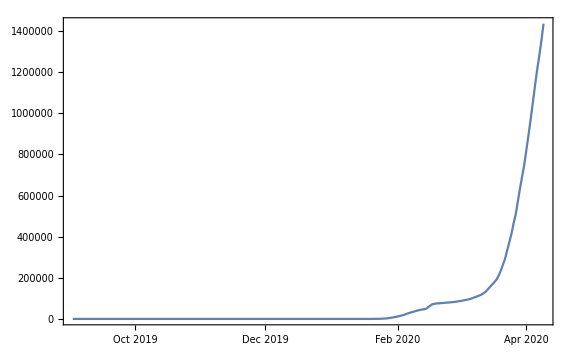

```mathematica
DateListPlot[confWORLD, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

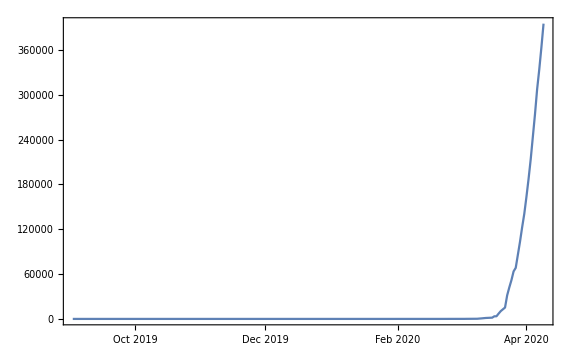

```mathematica
DateListPlot[confUSA, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

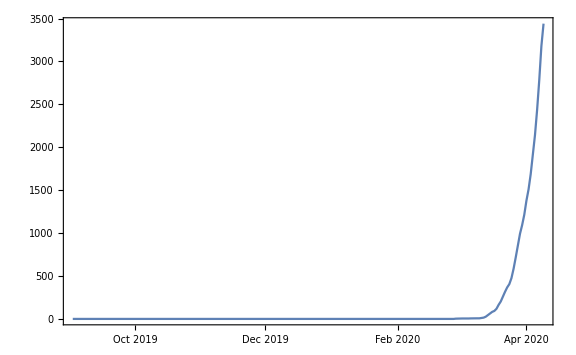

```mathematica
DateListPlot[confMEX, GridLines->Automatic,PlotRange->Full,ImageSize->Large] (*Tiene un pico el día final porque a la hora de captura de datos no se tiene registro de los nuevos casos*)
```

```mathematica
confMEXPos=GroupBy[Select[data,#["CONFIRMADOS MEXICO"]>0&],"CONFIRMADOS MEXICO"]
```

Dataset[<>]

```mathematica
dolarcierre=data[GroupBy["Fecha"], Total[DeleteCases[#,""]]&, "DOLAR CIERRE"];
```

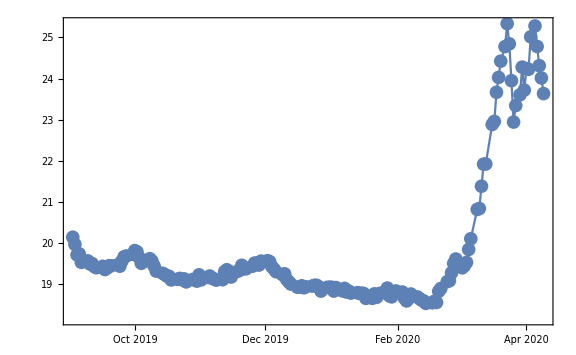

```mathematica
DateListPlot[dolarcierre,PlotMarkers->{Automatic,14}, GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

```mathematica
fecha=data[GroupBy["Fecha"]]
```

Dataset[<>]

```mathematica
dolarapertura=data[GroupBy["Fecha"],Total[DeleteCases[#,""]]&,"DOLAR APERTURA"]
```

Dataset[<>]

```mathematica
SmoothHistogram[dolarcierre,PlotRange->All,PlotTheme->"Marketing"]
SmoothHistogram[dolarapertura,PlotRange->All,PlotTheme->"Marketing"]
```

-Graphics-

-Graphics-

```mathematica
dolar=ListLinePlot[{dolarapertura,dolarcierre},PlotStyle->Thick,PlotRange->All,PlotLegends->Automatic,ImageSize->Full]
```

-Graphics-